```mathematica
Pitch - Class Set Theory
Based on The Structure of Atonal Music by Allen Forte
```

A pitch - class set is a set of distinct integers representing pitch classes.
	Cardinal number of a set - number of permutations
	Normal order - circular permutation for which difference between first and last is minimized.
  	Set must be in ascending order
Interval vectors - “ics” show interval content:
	There are 6 intervals, as follows:
	0=12
	1=11
	2=10
	 ....

```mathematica
(*generates random set. not used for demonstration atm*)
GenerateSet[notelen_,sl_]:=Module[{row=RandomSample[Range[0,sl],sl]},Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]]
```

```mathematica
(*don't do random ones*)
```

```mathematica
DynamicModule[{Wozzeck={1,2,3},
Schoenberg={2,3,4},
Strauss={4,5,7},
Random=RandomSample[Range[0,4],4]},Manipulate[
Column[{Style["Exploring Pitch-Class Set Theory", "Subsubtitle"],Text[Style[PCSet]],PlaySetChord[PCSet,length]}],{PCSet,{Wozzeck,Schoenberg,Strauss,Random->"Random"}},{length,1.2,3}]]
```

```mathematica
(*circular permutation:
,move first one to end, make sure to mod 12 them*)
```

```mathematica
(*goes through list; if some element is less than the first, add 12.
if an element is>12 and mod 12ing it would still make it bigger than first, then mod 12 it.*)
```

```mathematica
cperm[set_]:=Delete[Append[set,set[[1]]],1]
cpermordered[cp_]:=Table[If[cp[[i]]<cp[[1]],cp[[i]]+12,cp[[i]]],{i,1,Length[cp]}]
makeCPerm[pc_]:=cpermordered[cperm[pc]]
cperms[s_]:=NestList[makeCPerm,s,Length[s]-1]
normalOrder[s_]:=Sort[Table[{s[[i]],s[[i,Length[s]]]-s[[i,1]]},{i,1,Length[s]}],#1[[2]]<#2[[2]]&][[1,1]]
```

```mathematica
transpose[s_,n_]:=Table[s[[i]]+n,{i,1,Length[s]}]
inverse[s_]:=Table[Mod[12-s[[i]],12],{i,1,Length[s]}]
```

```mathematica
normalOrder[cperms[r]]
```

makeCPerm

```mathematica
primeForm[s_]:=Module[{t=-s[[1]]},transpose[normalOrder[cperms[s]],t]]
primeForm[r]
```

```mathematica
(*this is how you play a fucking chord*)
```

```mathematica
PlaySet[row_,notelen_]:=Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]
PlaySetChord[row_,notelen_]:=Sound[SoundNote[Table[row[[i]],{i,1,Length[row]}],notelen]]
```

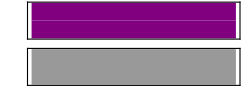

```mathematica
PlaySetChord[{1,2},1.2]
```